```mathematica
W1[x_,y_]:={Sin[x],Cos[y]}
```

```mathematica
h[x_,y_]:=5+Sin[x+y]
```

```mathematica
W2[x_,y_,t_]:=h[x,y,t]^3∇_{x,y} .(1/h[x,y,t] W1[x,y,t])
```

```mathematica
Simplify[W2[x,y]]
```

2 (9 Cos[x]+Cos[x+2 y]-9 Sin[y]+Sin[2 x+y])

### NSWE combined with Green-Naghdi

```mathematica
qs[x_,y_,t_]:={5+Sin[4x],Cos[5y-t],Sin[3y+t]}
```

```mathematica
qs[x_,y_,t_]:={1+1/5 Sin[4x+t],Cos[x-t],0}
```

```mathematica
qs[x_,y_,t_]:={1+0.2Sin[x-3t],Cos[y-2t],Sin[y+3t]}
```

```mathematica
qs[x_,y_,t_]:={2+Exp[Sin[x+y-t]],Cos[x-4t],Sin[y+4t]}
```

```mathematica
h[x_,y_,t_]:=qs[x,y,t][[1]]
```

```mathematica
b[x_,y_]:=-1
```

```mathematica
F1[x_,y_,t_]:={qs[x,y,t][[2]],qs[x,y,t][[2]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2,qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]]}
```

```mathematica
F2[x_,y_,t_]:={qs[x,y,t][[3]],qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]],qs[x,y,t][[3]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2}
```

```mathematica
temp1=Simplify[D[qs[x0,y0,t],t]+D[F1[x0,y0,t],x0]+D[F2[x0,y0,t],y0]+g h[x0,y0,t]{0,D[b[x0,y0], x0],D[b[x0,y0], y0]}]
```

{1/5 Cos[t+4 x0]+Sin[t-x0],-Sin[t-x0]+(5 Sin[2 (t-x0)])/(5+Sin[t+4 x0])+Cos[t+4 x0] ((4 g)/5+4/25 g Sin[t+4 x0]-(20 Cos[t-x0]^2)/(5+Sin[t+4 x0])^2),0}

```mathematica
CForm[temp1[[1]]]
```

Cos(t + 4*x0)/5. + Sin(t - x0)

```mathematica
CForm[temp1[[2]]]
```

-Sin(t - x0) + (5*Sin(2*(t - x0)))/(5 + Sin(t + 4*x0)) + 
   Cos(t + 4*x0)*((4*g)/5. + (4*g*Sin(t + 4*x0))/25. - 
      (20*Power(Cos(t - x0),2))/Power(5 + Sin(t + 4*x0),2))

```mathematica
CForm[temp1[[3]]]
```

0

```mathematica
W1[x_,y_,t_]:=1/α g h[x,y,t](∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[qs[x,y,t][[2]], t],D[qs[x,y,t][[3]], t]}
```

```mathematica
W1[x,y,t]
```

{Sin[t-x]+(4 g Cos[t+4 x] (1+1/5 Sin[t+4 x]))/(5 α),0}

```mathematica
W2[x_,y_,t_]:=h[x,y,t]^3∇_{x,y} .(1/h[x,y,t] W1[x,y,t])
```

```mathematica
CForm[W1[x,y,t]]
```

List(Sin(t - x) + (4*g*Cos(t + 4*x)*(1 + Sin(t + 4*x)/5.))/(5.*α),0)

```mathematica
CForm[W2[x,y,t]]
```

Power(1 + Sin(t + 4*x)/5.,3)*((-4*Cos(t + 4*x)*
        (Sin(t - x) + (4*g*Cos(t + 4*x)*(1 + Sin(t + 4*x)/5.))/(5.*α)))/
      (5.*Power(1 + Sin(t + 4*x)/5.,2)) + 
     (-Cos(t - x) + (16*g*Power(Cos(t + 4*x),2))/(25.*α) - 
        (16*g*(1 + Sin(t + 4*x)/5.)*Sin(t + 4*x))/(5.*α))/(1 + Sin(t + 4*x)/5.))

```mathematica
bGrad[x_,y_]:=∇_{x,y} b[x,y]
```

```mathematica
bGG=∇_{x,y} (∇_{x,y} b[x,y])
```

{{0,0},{0,0}}

```mathematica
ℛ1[W_]:=-1/(3h[x,y,t])∇_{x,y} (h[x,y,t]^3 W)-h[x,y,t]/2 W∇_{x,y} b[x,y]
```

```mathematica
ℛ12[W_]:=-h[x,y,t]/2 W∇_{x,y} b[x,y]
```

```mathematica
ℛ2[W_]:=1/(2h[x,y,t])∇_{x,y} (h[x,y,t]^2 W)+W∇_{x,y} b[x,y]
```

```mathematica
ℛ22[W_]:=W∇_{x,y} b[x,y]
```

```mathematica
𝒯[V_]:=ℛ1[∇_{x,y} .V]+ℛ2[∇_{x,y} b[x,y].V]
```

```mathematica
T2[V_]:=-h[x,y,t]^2/3 D[D[V, x], x]-h[x,y,t]D[h[x,y,t], x]D[V, x]+D[(h[x,y,t]+b[x,y]), x]D[b[x,y], x]V+h[x,y,t]/2 D[D[b[x,y], x], x]V
```

```mathematica
Q2[v1_]:=2h[x,y,t]D[(h[x,y,t]+b[x,y]/2), x](D[v1, x])^2+4/3 h[x,y,t]^2 D[v1, x]D[D[v1, x], x]+h[x,y,t]D[D[b[x,y], x], x]v1 D[v1, x]+(D[(h[x,y,t]+b[x,y]), x]D[D[b[x,y], x], x]+h[x,y,t]/2 D[D[D[b[x,y], x], x], x])v1^2
```

```mathematica
arg1[v1_,v2_]:={v1,v2}.bGG.{v1,v2}
```

```mathematica
argR1[x_,y_,t_]=arg1[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]
```

0

```mathematica
𝒬1[v1_,v2_]:=-2ℛ1[D[{v1,v2}, x].D[{-v2,v1}, y]+(∇_{x,y} .{v1,v2})^2]+ℛ2[argR1[x,y,t]]
```

```mathematica
𝒬12[v1_,v2_]:=-2ℛ12[D[{v1,v2}, x].D[{-v2,v1}, y]+(∇_{x,y} .{v1,v2})^2]+ℛ22[argR1[x,y,t]]
```

```mathematica
Ans1=
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-h[x,y,t]𝒬12[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]]
```

{1/7500(-2500 α Cos[5 x]+4500 α Cos[2 t+3 x]+34880 g Cos[t+4 x]-2880 g Cos[3 (t+4 x)]+7500 Sin[t-x]+2550 α Sin[t-x]+19456 g Sin[2 (t+4 x)]-128 g Sin[4 (t+4 x)]+875 α Sin[3 t+7 x]-675 α Sin[t+9 x]),0}

```mathematica
Ans1=
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])]
```

{1/7500(-2500 α Cos[5 x]+4500 α Cos[2 t+3 x]+34880 g Cos[t+4 x]-2880 g Cos[3 (t+4 x)]+7500 Sin[t-x]+2550 α Sin[t-x]+19456 g Sin[2 (t+4 x)]-128 g Sin[4 (t+4 x)]+875 α Sin[3 t+7 x]-675 α Sin[t+9 x]),0}

```mathematica
Ans2=
Simplify[W1[x,y,t][[1]]+α h[x,y,t]T2[1/h[x,y,t] W1[x,y,t][[1]]]-1/α g h[x,y,t] (D[h[x,y,t], x]+D[b[x,y], x])]
```

1/7500(-2500 α Cos[5 x]+4500 α Cos[2 t+3 x]+34880 g Cos[t+4 x]-2880 g Cos[3 (t+4 x)]+7500 Sin[t-x]+2550 α Sin[t-x]+19456 g Sin[2 (t+4 x)]-128 g Sin[4 (t+4 x)]+875 α Sin[3 t+7 x]-675 α Sin[t+9 x])

```mathematica
Simplify[Ans1[[1]]-Ans2]
```

0

```mathematica
Simplify[𝒬1[qs[x,y,t][[2]]/qs[x,y,t][[1]],0][[1]]-Q2[qs[x,y,t][[2]]/qs[x,y,t][[1]]]]
```

0

```mathematica
Q2[qs[x,y,t][[2]]/qs[x,y,t][[1]]]
```

8 Cos[4 x] (5+Sin[4 x]) ((4 Cos[4 x] Sin[t-x])/(5+Sin[4 x])^2+Cos[t-x]/(5+Sin[4 x]))^2+4/3 (5+Sin[4 x])^2 ((4 Cos[4 x] Sin[t-x])/(5+Sin[4 x])^2+Cos[t-x]/(5+Sin[4 x])) (-(32 Cos[4 x]^2 Sin[t-x])/(5+Sin[4 x])^3-(8 Cos[t-x] Cos[4 x])/(5+Sin[4 x])^2-(16 Sin[t-x] Sin[4 x])/(5+Sin[4 x])^2+Sin[t-x]/(5+Sin[4 x]))

```mathematica
CForm[Ans1[[1]]]
```

(-2500*α*Cos(5*x) + 4500*α*Cos(2*t + 3*x) + 34880*g*Cos(t + 4*x) - 
     2880*g*Cos(3*(t + 4*x)) + 7500*Sin(t - x) + 2550*α*Sin(t - x) + 
     19456*g*Sin(2*(t + 4*x)) - 128*g*Sin(4*(t + 4*x)) + 875*α*Sin(3*t + 7*x) - 
     675*α*Sin(t + 9*x))/7500.

```mathematica
CForm[Ans1[[2]]]
```

0.

### The case of non-flat bathymetry

```mathematica
qs[x_,y_,t_]:={5+Sin[4x],Cos[5y-t],Sin[3y+t]}
```

```mathematica
qs[x_,y_,t_]:={1+1/5 Sin[x-t],Cos[x-t],0}
```

```mathematica
qs[x_,y_,t_]:={1+0.2Sin[x-3t],Cos[y-2t],Sin[y+3t]}
```

```mathematica
qs[x_,y_,t_]:={2+Exp[Sin[x+y-t]],Cos[x-4t],Sin[y+4t]}
```

```mathematica
h[x_,y_,t_]:=qs[x,y,t][[1]]
```

```mathematica
b[x_,y_]:=-0.2Cos[x/2]
```

```mathematica
b[x_,y_]:=-1.
```

```mathematica
F1[x_,y_,t_]:={qs[x,y,t][[2]],qs[x,y,t][[2]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2,qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]]}
```

```mathematica
F2[x_,y_,t_]:={qs[x,y,t][[3]],qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]],qs[x,y,t][[3]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2}
```

```mathematica
temp1=Simplify[D[qs[x0,y0,t],t]+D[F1[x0,y0,t],x0]+D[F2[x0,y0,t],y0]+g h[x0,y0,t]{0,D[b[x0,y0], x0],D[b[x0,y0], y0]}]
```

{-1/5 Cos[t-x0]+Sin[t-x0],-(5 Cos[t-x0]^3)/(-5+Sin[t-x0])^2-1/25 g Cos[t-x0] (-5+Sin[t-x0])-Sin[t-x0]-(5 Sin[2 (t-x0)])/(-5+Sin[t-x0]),0}

```mathematica
CForm[temp1[[1]]]
```

-Cos(t - x0)/5. + Sin(t - x0)

```mathematica
CForm[temp1[[2]]]
```

(-5*Power(Cos(t - x0),3))/Power(-5 + Sin(t - x0),2) - 
   (g*Cos(t - x0)*(-5 + Sin(t - x0)))/25. - Sin(t - x0) - 
   (5*Sin(2*(t - x0)))/(-5 + Sin(t - x0))

```mathematica
CForm[temp1[[3]]]
```

0

```mathematica
W1[x_,y_,t_]:=1/α g h[x,y,t](∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[qs[x,y,t][[2]], t],D[qs[x,y,t][[3]], t]}
```

```mathematica
W1[x,y,t]
```

{Cos[t-x]+(g (4 Cos[4 x]+Sin[x]) (5+Sin[4 x]))/α,0}

```mathematica
W2[x_,y_,t_]:=h[x,y,t]^3∇_{x,y} .(1/h[x,y,t] W1[x,y,t])
```

```mathematica
CForm[W1[x,y,t]]
```

List(Cos(t - x) + (g*(4*Cos(4*x) + Sin(x))*(5 + Sin(4*x)))/α,0)

```mathematica
CForm[W2[x,y,t]]
```

Power(5 + Sin(4*x),3)*((-4*Cos(4*x)*
        (Cos(t - x) + (g*(4*Cos(4*x) + Sin(x))*(5 + Sin(4*x)))/α))/
      Power(5 + Sin(4*x),2) + (Sin(t - x) + 
        (4*g*Cos(4*x)*(4*Cos(4*x) + Sin(x)))/α + 
        (g*(Cos(x) - 16*Sin(4*x))*(5 + Sin(4*x)))/α)/(5 + Sin(4*x)))

```mathematica
bGrad[x_,y_]:=∇_{x,y} b[x,y]
```

```mathematica
bGG=∇_{x,y} (∇_{x,y} b[x,y])
```

{{Cos[x],0},{0,0}}

```mathematica
ℛ1[W_]:=-1/(3h[x,y,t])∇_{x,y} (h[x,y,t]^3 W)-h[x,y,t]/2 W∇_{x,y} b[x,y]
```

```mathematica
ℛ2[W_]:=1/(2h[x,y,t])∇_{x,y} (h[x,y,t]^2 W)+W∇_{x,y} b[x,y]
```

```mathematica
𝒯[V_]:=ℛ1[∇_{x,y} .V]+ℛ2[∇_{x,y} b[x,y].V]
```

```mathematica
T2[V_]:=-h[x,y,t]^2/3 D[D[V, x], x]-h[x,y,z]D[h[x,y,z], x]D[V, x]+D[(h[x,y,z]+b[x,y]), x]D[b[x,y], x]V+h[x,y,z]/2 D[D[b[x,y], x], x]V
```

```mathematica
Q2[v1_]:=2h[x,y,t]D[(h[x,y,t]+b[x,y]/2), x](D[v1, x])^2+4/3 h[x,y,t]^2 D[v1, x]D[D[v1, x], x]+h[x,y,t]D[D[b[x,y], x], x]v1 D[v1, x]+(D[(h[x,y,t]+b[x,y]), x]D[D[b[x,y], x], x]+h[x,y,t]/2 D[D[D[b[x,y], x], x], x])v1^2
```

```mathematica
arg1[v1_,v2_]:={v1,v2}.bGG.{v1,v2}
```

```mathematica
argR1[x_,y_,t_]=arg1[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]
```

(Cos[x] Sin[t-x]^2)/(5+Sin[4 x])^2

```mathematica
𝒬1[v1_,v2_]:=-2ℛ1[D[{v1,v2}, x].D[{-v2,v1}, y]+(∇_{x,y} .{v1,v2})^2]+ℛ2[argR1[x,y,t]]
```

```mathematica
Ans1=
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-h[x,y,t]𝒬1[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]]
```

{1/(6 (5+Sin[4 x])^2)(-3 Sin[t-x]^2 Sin[2 x] (5+Sin[4 x])+6 Cos[t-x] (5+Sin[4 x])^2+3/2 (Cos[t]+3 Cos[t-2 x]) Sin[t-x] (5+Sin[4 x])^2-1/8 (5+Sin[4 x])^2 (-60 α Cos[t]-108 α Cos[t-9 x]+12 α Cos[t-3 x]-60 α Cos[t-2 x]-432 α Cos[t-x]+6 g Cos[x]+420 g Cos[2 x]+492 g Cos[3 x]-140480 g Cos[4 x]+1932 g Cos[5 x]+540 g Cos[6 x]-6 g Cos[7 x]-106 g Cos[11 x]+11520 g Cos[12 x]+82 g Cos[13 x]+12 α Cos[t+x]-140 α Cos[t+7 x]+54 α Sin[t-6 x]-400 α Sin[t-5 x]-42 α Sin[t-4 x]-4220 g Sin[x]-306 g Sin[2 x]+60 g Sin[3 x]+45 g Sin[6 x]+1140 g Sin[7 x]-77920 g Sin[8 x]-660 g Sin[9 x]+51 g Sin[10 x]+512 g Sin[16 x]+42 α Sin[t+2 x]+720 α Sin[t+3 x]-54 α Sin[t+4 x])-1/4 (10 Cos[t-x]+3 Sin[t-5 x]+5 Sin[t+3 x]) (9 Cos[t-6 x]-640 Cos[t-5 x]-9 Cos[t-4 x]+15 Cos[t+2 x]+480 Cos[t+3 x]-15 Cos[t+4 x]+30 Sin[t]+36 Sin[t-9 x]-30 Sin[t-2 x]+216 Sin[t-x]+20 Sin[t+7 x])),0}

```mathematica
Ans1=
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])]
```

{9/4 α Cos[t-9 x]+(1+(17 α)/2) Cos[t-x]+1/12 (34880 g Cos[4 x]-2880 g Cos[12 x]+35 α Cos[t+7 x]+100 α Sin[t-5 x]+19456 g Sin[8 x]-128 g Sin[16 x]-180 α Sin[t+3 x]),0}

```mathematica
Ans2=
Simplify[W1[x,y,t][[1]]+α h[x,y,t]T2[1/h[x,y,t] W1[x,y,t][[1]]]-1/α g h[x,y,t] (D[h[x,y,t], x]+D[b[x,y], x])]
```

```mathematica
Simplify[𝒬1[qs[x,y,t][[2]]/qs[x,y,t][[1]],0][[1]]-Q2[qs[x,y,t][[2]]/qs[x,y,t][[1]]]]
```

0

```mathematica
Q2[qs[x,y,t][[2]]/qs[x,y,t][[1]]]
```

8 Cos[4 x] (5+Sin[4 x]) ((4 Cos[4 x] Sin[t-x])/(5+Sin[4 x])^2+Cos[t-x]/(5+Sin[4 x]))^2+4/3 (5+Sin[4 x])^2 ((4 Cos[4 x] Sin[t-x])/(5+Sin[4 x])^2+Cos[t-x]/(5+Sin[4 x])) (-(32 Cos[4 x]^2 Sin[t-x])/(5+Sin[4 x])^3-(8 Cos[t-x] Cos[4 x])/(5+Sin[4 x])^2-(16 Sin[t-x] Sin[4 x])/(5+Sin[4 x])^2+Sin[t-x]/(5+Sin[4 x]))

```mathematica
CForm[Ans1[[1]]]
```

(9*α*Cos(t - 9*x))/4. + (1 + (17*α)/2.)*Cos(t - x) + 
   (34880*g*Cos(4*x) - 2880*g*Cos(12*x) + 35*α*Cos(t + 7*x) + 
      100*α*Sin(t - 5*x) + 19456*g*Sin(8*x) - 128*g*Sin(16*x) - 
      180*α*Sin(t + 3*x))/12.

```mathematica
CForm[Ans1[[2]]]
```

0.

### When the depression hits and you decide to go 1D

```mathematica
qs[x_,y_,t_]:={1+1/5 Sin[4x+t],Cos[x-t],0}
```

```mathematica
h[x_,y_,t_]:=qs[x,y,t][[1]]
```

```mathematica
b[x_,y_]:=-1
```

```mathematica
W1[x_,y_,t_]:=1/α g h[x,y,t](∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[qs[x,y,t][[2]], t],D[qs[x,y,t][[3]], t]}
```

```mathematica
bGG=∇_{x,y} (∇_{x,y} b[x,y])
```

{{0,0},{0,0}}

```mathematica
ℛ1[W_]:=-1/(3h[x,y,t])∇_{x,y} (h[x,y,t]^3 W)-h[x,y,t]/2 W∇_{x,y} b[x,y]
```

```mathematica
ℛ2[W_]:=1/(2h[x,y,t])∇_{x,y} (h[x,y,t]^2 W)+W∇_{x,y} b[x,y]
```

```mathematica
𝒯[V_]:=ℛ1[∇_{x,y} .V]+ℛ2[∇_{x,y} b[x,y].V]
```

```mathematica
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[(qs[x,y,t][[2]]/qs[x,y,t][[1]]), x]*D[(qs[x,y,t][[2]]/qs[x,y,t][[1]]), x],0}]
```

```mathematica
Simplify[W1[x,y,t]+α h[x,y,t]𝒯[1/h[x,y,t] W1[x,y,t]]-1/α g h[x,y,t] (∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[(qs[x,y,t][[2]]/qs[x,y,t][[1]]), x,x],0}]
```

{1/(60000 (5+Sin[t+4 x])^3)(450000 Cos[t-x]-750 (-3030+2957 α) Cos[5 x]-2272500 Cos[2 t+3 x]+4338150 α Cos[2 t+3 x]+41888640 g Cos[t+4 x]-10033152 g Cos[3 (t+4 x)]+144640 g Cos[5 (t+4 x)]-128 g Cos[7 (t+4 x)]-1875000 Cos[3 t+7 x]-675000 Cos[t+9 x]+7500 Cos[4 t+11 x]-397575 α Cos[4 t+11 x]-7500 Cos[2 t+13 x]+276975 α Cos[2 t+13 x]+875 α Cos[6 t+19 x]-675 α Cos[4 t+21 x]+7950000 Sin[t-x]+535500 α Sin[t-x]-16500000 Sin[5 x]-30750 α Sin[5 (t+3 x)]-4500000 Sin[2 t+3 x]+32033600 g Sin[2 (t+4 x)]-1626880 g Sin[4 (t+4 x)]+6720 g Sin[6 (t+4 x)]-225000 Sin[3 t+7 x]+2217000 α Sin[3 t+7 x]+225000 Sin[t+9 x]-1401000 α Sin[t+9 x]+22750 α Sin[3 t+17 x]),0}

```mathematica
CForm[%]
```

List((450000*Cos(t - x) - 750*(-3030 + 2957*α)*Cos(5*x) - 
      2272500*Cos(2*t + 3*x) + 4338150*α*Cos(2*t + 3*x) + 
      41888640*g*Cos(t + 4*x) - 10033152*g*Cos(3*(t + 4*x)) + 
      144640*g*Cos(5*(t + 4*x)) - 128*g*Cos(7*(t + 4*x)) - 
      1875000*Cos(3*t + 7*x) - 675000*Cos(t + 9*x) + 7500*Cos(4*t + 11*x) - 
      397575*α*Cos(4*t + 11*x) - 7500*Cos(2*t + 13*x) + 
      276975*α*Cos(2*t + 13*x) + 875*α*Cos(6*t + 19*x) - 
      675*α*Cos(4*t + 21*x) + 7950000*Sin(t - x) + 535500*α*Sin(t - x) - 
      16500000*Sin(5*x) - 30750*α*Sin(5*(t + 3*x)) - 4500000*Sin(2*t + 3*x) + 
      32033600*g*Sin(2*(t + 4*x)) - 1626880*g*Sin(4*(t + 4*x)) + 
      6720*g*Sin(6*(t + 4*x)) - 225000*Sin(3*t + 7*x) + 
      2217000*α*Sin(3*t + 7*x) + 225000*Sin(t + 9*x) - 1401000*α*Sin(t + 9*x) + 
      22750*α*Sin(3*t + 17*x))/(60000.*Power(5 + Sin(t + 4*x),3)),0)

### Testing the new extended form of Q1

```mathematica
qs[x_,y_,t_]:={5+Sin[4x],Cos[5y-t],Sin[3y+t]}
```

```mathematica
qs[x_,y_,t_]:={1+1/5 Sin[4x+t],Cos[x-t],0}
```

```mathematica
qs[x_,y_,t_]:={1+0.2Sin[x-3t],Cos[y-2t],Sin[y+3t]}
```

```mathematica
qs[x_,y_,t_]:={2+Exp[Sin[x+y-t]],Cos[x-4t],Sin[y+4t]}
```

```mathematica
h[x_,y_,t_]:=qs[x,y,t][[1]]
```

```mathematica
b[x_,y_]:=Sin[x+y]
```

```mathematica
b[x_,y_]:=-1
```

```mathematica
F1[x_,y_,t_]:={qs[x,y,t][[2]],qs[x,y,t][[2]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2,qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]]}
```

```mathematica
F2[x_,y_,t_]:={qs[x,y,t][[3]],qs[x,y,t][[2]]*qs[x,y,t][[3]]/qs[x,y,t][[1]],qs[x,y,t][[3]]^2/qs[x,y,t][[1]]+g/2*qs[x,y,t][[1]]^2}
```

```mathematica
temp1=Simplify[D[qs[x0,y0,t],t]+D[F1[x0,y0,t],x0]+D[F2[x0,y0,t],y0]+g h[x0,y0,t]{0,D[b[x0,y0], x0],D[b[x0,y0], y0]}]
```

{1/5 Cos[t+4 x0]+Sin[t-x0],-Sin[t-x0]+(5 Sin[2 (t-x0)])/(5+Sin[t+4 x0])+Cos[t+4 x0] ((4 g)/5+4/25 g Sin[t+4 x0]-(20 Cos[t-x0]^2)/(5+Sin[t+4 x0])^2),0}

```mathematica
CForm[temp1[[1]]]
```

Cos(t + 4*x0)/5. + Sin(t - x0)

```mathematica
CForm[temp1[[2]]]
```

-Sin(t - x0) + (5*Sin(2*(t - x0)))/(5 + Sin(t + 4*x0)) + 
   Cos(t + 4*x0)*((4*g)/5. + (4*g*Sin(t + 4*x0))/25. - 
      (20*Power(Cos(t - x0),2))/Power(5 + Sin(t + 4*x0),2))

```mathematica
CForm[temp1[[3]]]
```

0

```mathematica
W1[x_,y_,t_]:=1/α g h[x,y,t](∇_{x,y} h[x,y,t]+∇_{x,y} b[x,y])-{D[qs[x,y,t][[2]], t],D[qs[x,y,t][[3]], t]}
```

```mathematica
W1[x,y,t]
```

{Sin[t-x]+(4 g Cos[t+4 x] (1+1/5 Sin[t+4 x]))/(5 α),0}

```mathematica
W2[x_,y_,t_]:=h[x,y,t]^3∇_{x,y} .(1/h[x,y,t] W1[x,y,t])
```

```mathematica
CForm[W1[x,y,t]]
```

List(Sin(t - x) + (4*g*Cos(t + 4*x)*(1 + Sin(t + 4*x)/5.))/(5.*α),0)

```mathematica
CForm[W2[x,y,t]]
```

Power(1 + Sin(t + 4*x)/5.,3)*((-4*Cos(t + 4*x)*
        (Sin(t - x) + (4*g*Cos(t + 4*x)*(1 + Sin(t + 4*x)/5.))/(5.*α)))/
      (5.*Power(1 + Sin(t + 4*x)/5.,2)) + 
     (-Cos(t - x) + (16*g*Power(Cos(t + 4*x),2))/(25.*α) - 
        (16*g*(1 + Sin(t + 4*x)/5.)*Sin(t + 4*x))/(5.*α))/(1 + Sin(t + 4*x)/5.))

```mathematica
bGrad[x_,y_]:=∇_{x,y} b[x,y]
```

```mathematica
bGG=∇_{x,y} (∇_{x,y} b[x,y])
```

{{0,0},{0,0}}

```mathematica
ℛ1[W_]:=-1/(3h[x,y,t])∇_{x,y} (h[x,y,t]^3 W)-h[x,y,t]/2 W∇_{x,y} b[x,y]
```

```mathematica
ℛ2[W_]:=1/(2h[x,y,t])∇_{x,y} (h[x,y,t]^2 W)+W∇_{x,y} b[x,y]
```

```mathematica
𝒯[V_]:=ℛ1[∇_{x,y} .V]+ℛ2[∇_{x,y} b[x,y].V]
```

```mathematica
T2[V_]:=-h[x,y,t]^2/3 D[D[V, x], x]-h[x,y,t]D[h[x,y,t], x]D[V, x]+D[(h[x,y,t]+b[x,y]), x]D[b[x,y], x]V+h[x,y,t]/2 D[D[b[x,y], x], x]V
```

```mathematica
Q2[v1_]:=2h[x,y,t]D[(h[x,y,t]+b[x,y]/2), x](D[v1, x])^2+4/3 h[x,y,t]^2 D[v1, x]D[D[v1, x], x]+h[x,y,t]D[D[b[x,y], x], x]v1 D[v1, x]+(D[(h[x,y,t]+b[x,y]), x]D[D[b[x,y], x], x]+h[x,y,t]/2 D[D[D[b[x,y], x], x], x])v1^2
```

```mathematica
arg1[v1_,v2_]:={v1,v2}.bGG.{v1,v2}
```

```mathematica
argR1[x_,y_,t_]=arg1[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]
```

0

```mathematica
𝒬1[v1_,v2_]:=-2ℛ1[D[{v1,v2}, x].D[{-v2,v1}, y]+(∇_{x,y} .{v1,v2})^2]+ℛ2[argR1[x,y,t]]
```

```mathematica
h1:=h[x,y,t]
```

```mathematica
b1:=b[x,y]
```

```mathematica
test1[v1_,v2_]:=∇_{x,y} (h1^3 D[{v1,v2}, x].D[{-v2,v1}, y]+h1^3(∇_{x,y} .{v1,v2})^2)
```

```mathematica
test2[v1_,v2_]:={3 h1^2 D[h1, x](-D[v1, x]D[v2, y]+D[v2, x]D[v1, y]+(D[v1, x]+D[v2, y])^2)+h1^3(-D[v1, x,x]D[v2, y]+D[v2, x,x]D[v1, y]+2(D[v1, x]+D[v2, y])(D[v1, x,x]+D[v2, x,y])-D[v1, x]D[v2, y,x]+D[v2, x]D[v1, x,y]),3 h1^2 D[h1, y](-D[v1, x]D[v2, y]+D[v2, x]D[v1, y]+(D[v1, x]+D[v2, y])^2)+h1^3(-D[v1, x,y]D[v2, y]+D[v2, x,y]D[v1, y]+2(D[v1, x]+D[v2, y])(D[v1, x,y]+D[v2, y,y])-D[v1, x]D[v2, y,y]+D[v2, x]D[v1, y,y])}
```

```mathematica
test3[v1_,v2_]:=∇_{x,y} (h1^2{v1,v2}.∇_{x,y} ∇_{x,y} b1.{v1,v2})
```

```mathematica
test4[v1_,v2_]:={2h1 D[h1, x](v1^2 D[b1, x,x]+2v1 v2 D[b1, x,y]+v2^2 D[b1, y,y])+h1^2(2v1 D[v1, x]D[b1, x,x]+v1^2 D[b1, x,x,x]+2 D[v1, x] v2 D[b1, x,y]+2v1 D[v2, x]D[b1, x,y]+2v1 v2 D[b1, x,y,x]+2v2 D[v2, x]D[b1, y,y]+v2^2 D[b1, y,y,x]),2h1 D[h1, y](v1^2 D[b1, x,x]+2v1 v2 D[b1, x,y]+v2^2 D[b1, y,y])+h1^2(2v1 D[v1, y]D[b1, x,x]+v1^2 D[b1, x,x,y]+2 D[v1, y] v2 D[b1, x,y]+2v1 D[v2, y]D[b1, x,y]+2v1 v2 D[b1, x,y,y]+2v2 D[v2, y]D[b1, y,y]+v2^2 D[b1, y,y,y])}
```

```mathematica
Simplify[test2[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{-1/125 Sin[t-x] (10 Cos[t-x]+7 Sin[5 x]-5 Sin[2 t+3 x]) (5+Sin[t+4 x])^2,0}

```mathematica
Simplify[test2[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{108 Cos[4 x] Cos[t+3 y]^2 (5+Sin[4 x])^2,-27 (5+Sin[4 x])^3 Sin[2 (t+3 y)]}

```mathematica
Simplify[test3[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{-1/2 (5+Sin[4 x]) (Cos[t-y]+Sin[t-y])^2 (Cos[4 y]+Sin[4 y])^2 (10 Cos[x+y]-7 Sin[3 x-y]+9 Sin[5 x+y]),-1/2 (5+Sin[4 x])^2 (Cos[t-y]+Sin[t-y]) (Cos[4 y]+Sin[4 y]) (11 Cos[t-x-6 y]-9 Cos[t+x-4 y]-5 Sin[t-x+2 y]+7 Sin[t+x+4 y])}

```mathematica
Simplify[test4[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{-1/2 (5+Sin[4 x]) (Cos[t-y]+Sin[t-y])^2 (Cos[4 y]+Sin[4 y])^2 (10 Cos[x+y]-7 Sin[3 x-y]+9 Sin[5 x+y]),-1/2 (5+Sin[4 x])^2 (Cos[t-y]+Sin[t-y]) (Cos[4 y]+Sin[4 y]) (11 Cos[t-x-6 y]-9 Cos[t+x-4 y]-5 Sin[t-x+2 y]+7 Sin[t+x+4 y])}

```mathematica
Simplify[test1[qs[x,y,t][[2]],qs[x,y,t][[3]]]-test2[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{0,0}

```mathematica
Simplify[test3[qs[x,y,t][[2]],qs[x,y,t][[3]]]-test4[qs[x,y,t][[2]],qs[x,y,t][[3]]]]
```

{0,0}

```mathematica
FullSimplify[2/3 test2[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]+1/2 test4[qs[x,y,t][[2]]/qs[x,y,t][[1]],qs[x,y,t][[3]]/qs[x,y,t][[1]]]]
```

{1/(30 (5+Sin[t+4 x])^2)(3 Cos[5 x]+5 (Cos[2 t+3 x]-2 Sin[t-x])) (54 Cos[t-x]+5 Cos[3 t+7 x]+9 Cos[t+9 x]-40 (4 Sin[5 x]+3 Sin[2 t+3 x])),0}

```mathematica
CForm[%]
```

List(((3*Cos(5*x) + 5*(Cos(2*t + 3*x) - 2*Sin(t - x)))*
      (54*Cos(t - x) + 5*Cos(3*t + 7*x) + 9*Cos(t + 9*x) - 
        40*(4*Sin(5*x) + 3*Sin(2*t + 3*x))))/(30.*Power(5 + Sin(t + 4*x),2)),0)

### An analytical solution for GN equation

```mathematica
aGN=0.07
```

0.07

```mathematica
h0GN=0.7
```

0.7

```mathematica
kappaGN=(√(3aGN))/(2h0GN √(h0GN+aGN))
```

0.373024

```mathematica
gGN=9.81
```

9.81

```mathematica
x0GN=-1
```

-1

```mathematica
cGN=√(gGN(h0GN+aGN))
```

2.7484

```mathematica
h[x_,y_,t_]:=h0GN+aGN/(Cosh[kappaGN(x-x0GN-cGN t)])^2
```

```mathematica
hu[x_,y_,t_]:=cGN h[x,y,t]-cGN h0GN
```

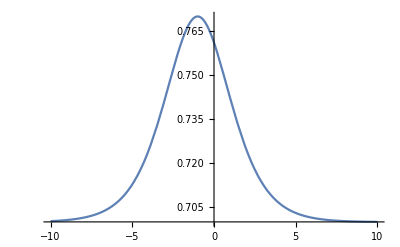

```mathematica
Plot[h[x,0,0],{x,-10.,10.}]
```

```mathematica
hu[-10,0,0]
```

1.21355×10^-7

### A bathymetry function for 2D problem

```mathematica
gradb=Grad[1/4 Cos[Pi/2 r],{r,θ},"Polar"]
```

{-1/8 π Sin[(π r)/2],0}

```mathematica
TransformedField["Polar"->"Cartesian",gradb,{r,θ}->{x,y}]//FullSimplify
```

{-(π x Sin[1/2 π √(x^2+y^2)])/(8 √(x^2+y^2)),-(π y Sin[1/2 π √(x^2+y^2)])/(8 √(x^2+y^2))}

```mathematica
gradgradb=Grad[gradb,{r,θ},"Polar"]
```

{{-1/16 π^2 Cos[(π r)/2],0},{0,-(π Sin[(π r)/2])/(8 r)}}

```mathematica
TransformedField["Polar"->"Cartesian",gradgradb,{r,θ}->{x,y}]//FullSimplify
```

{{-(π (π x^2 √(x^2+y^2) Cos[1/2 π √(x^2+y^2)]+2 y^2 Sin[1/2 π √(x^2+y^2)]))/(16 (x^2+y^2)^(3/2)),-(π x y (π √(x^2+y^2) Cos[1/2 π √(x^2+y^2)]-2 Sin[1/2 π √(x^2+y^2)]))/(16 (x^2+y^2)^(3/2))},{-(π x y (π √(x^2+y^2) Cos[1/2 π √(x^2+y^2)]-2 Sin[1/2 π √(x^2+y^2)]))/(16 (x^2+y^2)^(3/2)),-(π (π y^2 √(x^2+y^2) Cos[1/2 π √(x^2+y^2)]+2 x^2 Sin[1/2 π √(x^2+y^2)]))/(16 (x^2+y^2)^(3/2))}}

```mathematica
TransformedField["Polar"->"Cartesian",gradgradgradb,{r,θ}->{x,y}]//FullSimplify
```

{{{(π x (-6 π y^2 (x^2+y^2) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (12 y^2+π^2 x^2 (x^2+y^2)) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3),(π y (2 π (2 x^4+x^2 y^2-y^4) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 y^2+x^2 (-8+π^2 (x^2+y^2))) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3)},{(π y (2 π (2 x^4+x^2 y^2-y^4) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 y^2+x^2 (-8+π^2 (x^2+y^2))) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3),(π x (-2 π (x^2-2 y^2) (x^2+y^2) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 x^2+(-8+π^2 x^2) y^2+π^2 y^4) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3)}},{{(π y (2 π (2 x^4+x^2 y^2-y^4) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 y^2+x^2 (-8+π^2 (x^2+y^2))) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3),(π x (-2 π (x^2-2 y^2) (x^2+y^2) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 x^2+(-8+π^2 x^2) y^2+π^2 y^4) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3)},{(π x (-2 π (x^2-2 y^2) (x^2+y^2) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (4 x^2+(-8+π^2 x^2) y^2+π^2 y^4) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3),(π y (-6 π x^2 (x^2+y^2) Cos[1/2 π √(x^2+y^2)]+√(x^2+y^2) (π^2 y^4+x^2 (12+π^2 y^2)) Sin[1/2 π √(x^2+y^2)]))/(32 (x^2+y^2)^3)}}}

```mathematica
gradgradgradb=Grad[gradgradb,{r,θ},"Polar"]
```

{{{1/32 π^3 Sin[(π r)/2],0},{0,(-1/16 π^2 Cos[(π r)/2]+(π Sin[(π r)/2])/(8 r))/r}},{{0,(-1/16 π^2 Cos[(π r)/2]+(π Sin[(π r)/2])/(8 r))/r},{-(π^2 Cos[(π r)/2])/(16 r)+(π Sin[(π r)/2])/(8 r^2),0}}}

```mathematica
bath[x_,y_]:=1/8(1+Cos[Pi/2(√((x-2)^2+y^2))])
```

```mathematica
Plot3D[bath[x,y],{x,0,4},{y,-2,2}]
```

-Graphics3D-

```mathematica
FullSimplify[∇_{x,y} bath[x,y]/.{(x-2)^2+y^2->r^2}]
```

{-(π (-2+x) Sin[(π r)/2])/(16 r),-(π y Sin[(π r)/2])/(16 r)}

```mathematica
FullSimplify[∇_{x,y} ∇_{x,y} bath[x,y]/.{(x-2)^2+y^2->r^2,x-2->x2}]
```

{{-(π (π r x2^2 Cos[(π r)/2]+2 (r-x2) (r+x2) Sin[(π r)/2]))/(32 r^3),-(π x2 y (π r Cos[(π r)/2]-2 Sin[(π r)/2]))/(32 r^3)},{-(π x2 y (π r Cos[(π r)/2]-2 Sin[(π r)/2]))/(32 r^3),-(π (π r y^2 Cos[(π r)/2]+2 (r-y) (r+y) Sin[(π r)/2]))/(32 r^3)}}

```mathematica
CForm[%]
```

List(List(-(Pi*(Pi*r*Power(x2,2)*Cos((Pi*r)/2.) + 
          2*(r - x2)*(r + x2)*Sin((Pi*r)/2.)))/(16.*Power(r,3)),
    -(Pi*x2*y*(Pi*r*Cos((Pi*r)/2.) - 2*Sin((Pi*r)/2.)))/(16.*Power(r,3))),
   List(-(Pi*x2*y*(Pi*r*Cos((Pi*r)/2.) - 2*Sin((Pi*r)/2.)))/(16.*Power(r,3)),
    -(Pi*(Pi*r*Power(y,2)*Cos((Pi*r)/2.) + 2*(r - y)*(r + y)*Sin((Pi*r)/2.)))/
     (16.*Power(r,3))))

```mathematica
FullSimplify[∇_{x,y} ∇_{x,y} ∇_{x,y} bath[x,y]/.{(x-2)^2+y^2->r^2,x-2->x2}]
```

{{{(π x2 (6 π r (-r^2+x2^2) Cos[(π r)/2]+(-12 x2^2+r^2 (12+π^2 x2^2)) Sin[(π r)/2]))/(64 r^5),(π y (-2 π r (r^2-3 x2^2) Cos[(π r)/2]+(-12 x2^2+r^2 (4+π^2 x2^2)) Sin[(π r)/2]))/(64 r^5)},{(π y (-2 π r (r^2-3 x2^2) Cos[(π r)/2]+(-12 x2^2+r^2 (4+π^2 x2^2)) Sin[(π r)/2]))/(64 r^5),(π x2 (-2 π r (r^2-3 y^2) Cos[(π r)/2]+(-12 y^2+r^2 (4+π^2 y^2)) Sin[(π r)/2]))/(64 r^5)}},{{(π y (-2 π r (r^2-3 x2^2) Cos[(π r)/2]+(-12 x2^2+r^2 (4+π^2 x2^2)) Sin[(π r)/2]))/(64 r^5),(π x2 (-2 π r (r^2-3 y^2) Cos[(π r)/2]+(-12 y^2+r^2 (4+π^2 y^2)) Sin[(π r)/2]))/(64 r^5)},{(π x2 (-2 π r (r^2-3 y^2) Cos[(π r)/2]+(-12 y^2+r^2 (4+π^2 y^2)) Sin[(π r)/2]))/(64 r^5),(π y (6 π r (-r^2+y^2) Cos[(π r)/2]+(-12 y^2+r^2 (12+π^2 y^2)) Sin[(π r)/2]))/(64 r^5)}}}

```mathematica
CForm[%]
```

List(List(List((Pi*x2*(6*Pi*r*(-Power(r,2) + Power(x2,2))*Cos((Pi*r)/2.) + 
          (-12*Power(x2,2) + Power(r,2)*(12 + Power(Pi,2)*Power(x2,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)),
     (Pi*y*(-2*Pi*r*(Power(r,2) - 3*Power(x2,2))*Cos((Pi*r)/2.) + 
          (-12*Power(x2,2) + Power(r,2)*(4 + Power(Pi,2)*Power(x2,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5))),
    List((Pi*y*(-2*Pi*r*(Power(r,2) - 3*Power(x2,2))*Cos((Pi*r)/2.) + 
          (-12*Power(x2,2) + Power(r,2)*(4 + Power(Pi,2)*Power(x2,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)),
     (Pi*x2*(-2*Pi*r*(Power(r,2) - 3*Power(y,2))*Cos((Pi*r)/2.) + 
          (-12*Power(y,2) + Power(r,2)*(4 + Power(Pi,2)*Power(y,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)))),
   List(List((Pi*y*(-2*Pi*r*(Power(r,2) - 3*Power(x2,2))*Cos((Pi*r)/2.) + 
          (-12*Power(x2,2) + Power(r,2)*(4 + Power(Pi,2)*Power(x2,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)),
     (Pi*x2*(-2*Pi*r*(Power(r,2) - 3*Power(y,2))*Cos((Pi*r)/2.) + 
          (-12*Power(y,2) + Power(r,2)*(4 + Power(Pi,2)*Power(y,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5))),
    List((Pi*x2*(-2*Pi*r*(Power(r,2) - 3*Power(y,2))*Cos((Pi*r)/2.) + 
          (-12*Power(y,2) + Power(r,2)*(4 + Power(Pi,2)*Power(y,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)),
     (Pi*y*(6*Pi*r*(-Power(r,2) + Power(y,2))*Cos((Pi*r)/2.) + 
          (-12*Power(y,2) + Power(r,2)*(12 + Power(Pi,2)*Power(y,2)))*
           Sin((Pi*r)/2.)))/(32.*Power(r,5)))))

### Another analytical solution for GN equation

```mathematica
gGN=9.81
```

9.81

```mathematica
h0GN=0.7
```

0.7

```mathematica
a0GN=0.07
```

0.07

```mathematica
η=-0.06
```

-0.06

```mathematica
δ=0.1
```

0.1

```mathematica
Clear[x1]
```

```mathematica
Solve[2η x1^6-(3η+1/3+2η δ)x1^4+2δ(η+1/3)x1^2+η+1/3==0,x1]
```

{{x1→-2.14094},{x1→-1.05163},{x1→0.-0.869603 ⅈ},{x1→0.+0.869603 ⅈ},{x1→1.05163},{x1→2.14094}}

```mathematica
cGN=Sqrt[gGN*(h0GN+a0GN)]
```

2.7484

```mathematica
aGN=(cGN^2-gGN h0GN)/cGN
```

0.249855

```mathematica
bGN=((cGN^2-gGN h0GN)/(4((η+1/3)gGN h0GN^3-η h0GN^2 cGN^2)))^(1/2)
```

0.387756

```mathematica
0.3877561571610474
```

```mathematica
bGN=kappaGN
```

0.373024

```mathematica
a1GN=(cGN^2-gGN h0GN)/(3((η+1/3)gGN h0GN-η cGN^2))h0GN
```

0.0687623

```mathematica
a2GN=((cGN^2-gGN h0GN)^2)/(2gGN h0GN cGN^2) ((η+1/3)gGN h0GN+2η cGN^2)/((η+1/3)gGN h0GN-η cGN^2)h0GN
```

0.00132524

```mathematica
uGN[x_,t_]:=aGN Sech[bGN(x-cGN t)]^2
```

```mathematica
hGN[x_,t_]:=a1GN Sech[bGN (x-cGN t)]^2+a2GN Sech[bGN(x-cGN t)]^4
```

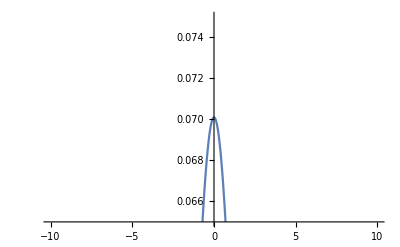

```mathematica
Plot[hGN[x,0],{x,-10.,10.},PlotRange->{0.065,0.075}]
```